# Energy Conditions

## Null Conditions

```mathematica
(*We use the equation ρ + p ≥ 0, for each case*)
```

## Mass Cases

### Γ = 1 and K = 1

```mathematica
mp1=NDSolveValue[{-16 π^2 m'[r] (6 (3 m[r]+r (-1+m'[r])) m'[r]+r (3 r+r^3 Λ-6 m[r]) m''[r])==0/.Λ->10^-52,m[0.001]==10^-5,m[9000]==0.1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

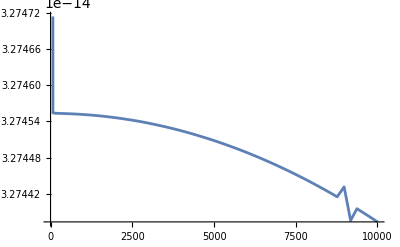

```mathematica
Plot[mp1[r]/(4 π r^2),{r,0,10000}]
```

```mathematica
(*For this case ρ and p are the same since Γ and K = 1. Since ρ is greater than 0 ρ + p must also be greater than 0*)
```

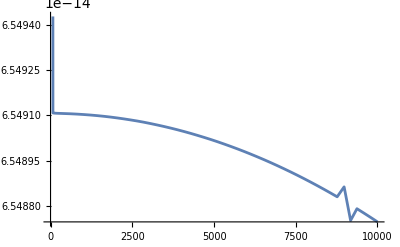

```mathematica
Plot[mp1[r]/(4 π r^2)+mp1[r]/(4 π r^2),{r,0,10000}]
```

### K = r, Γ = 1

```mathematica
mp2=NDSolveValue[{-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52},m[0.001]==10^-5,m[9000]==1},m',{r,0.0001,9000}]
```

InterpolatingFunction[…]

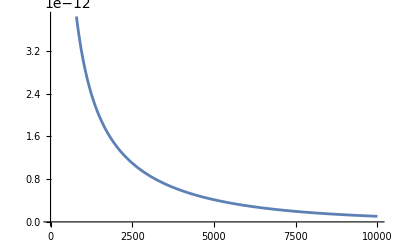

```mathematica
Plot[mp2[r]/(4 π r^2),{r,0.1,10000}]
```

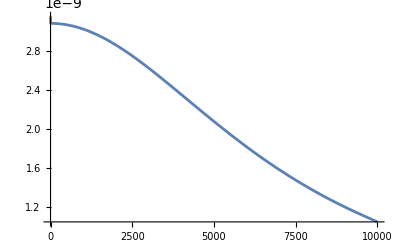

```mathematica
Plot[r(mp2[r]/(4 π r^2)),{r,0.1,10000}]
```

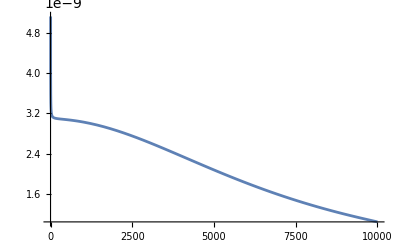

```mathematica
Plot[mp2[r]/(4 π r^2)+r(mp2[r]/(4 π r^2)),{r,0.1,10000}]
```

### K = r/b, Γ = 1

```mathematica
mp3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==0,m[9000]==1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

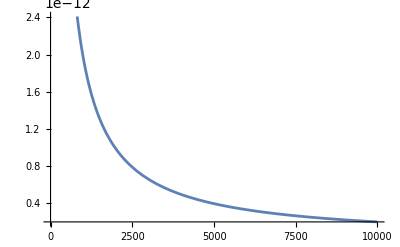

```mathematica
Plot[mp3[r]/(4 π r^2),{r,0,10000}]
```

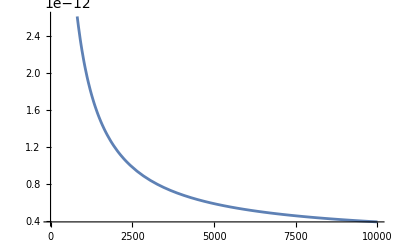

```mathematica
Plot[(mp3[r]/(4 π r^2))r/10000+(mp3[r]/(4 π r^2)),{r,0,10000}]
```

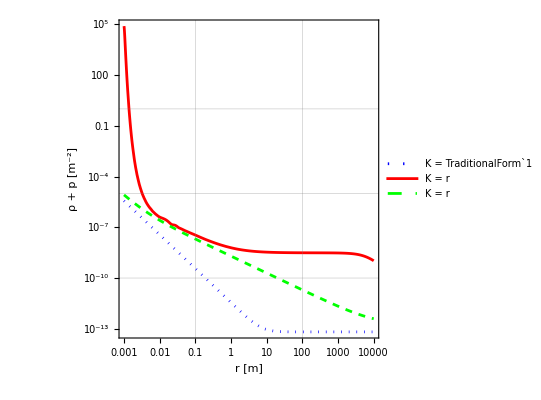

```mathematica
nulldenKas=LogLogPlot[{(mp1[r]/(4 π r^2)+mp1[r]/(4 π r^2)) ,(mp2[r]/(4 π r^2)+r(mp2[r]/(4 π r^2))) ,(mp3[r]/(4 π r^2)+(mp3[r]/(4 π r^2))r/10000)},{r,0.001,10000},FrameTicks->{{All,None},{All,None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain], "ρ + p"  Style["[m^-2]",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = TraditionalForm`1" ,"K = r" ,"K = r" },{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

## Γ Cases

### K = 1 and ρ = ρ_0

```mathematica
gd1=NDSolveValue[{(3 (4 π)^(1+2 Γ[r]) r Subscript[ρ, 0]^(2 Γ[r])+r Subscript[ρ, 0] (16^Γ[r] π^(2 Γ[r]) Λ+(4 π)^(1+2 Γ[r]) Subscript[ρ, 0])+16^Γ[r] π^(2 Γ[r]) Subscript[ρ, 0]^Γ[r] (r (Λ+16 π Subscript[ρ, 0])+Log[Subscript[ρ, 0]] (3+r^2 Λ-8 π r^2 Subscript[ρ, 0]) Γ'[r]))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

InterpolatingFunction[…]

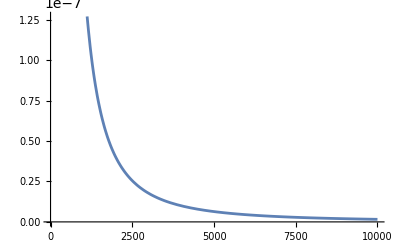

```mathematica
Plot[(10^-22)^gd1[r],{r,0,10000}]
```

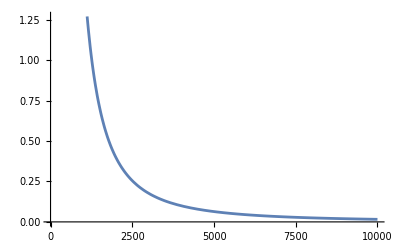

```mathematica
Plot[((10^-22)^gd1[r]+10^-22) 10^7,{r,0,10000}]
```

### K = 1 and ρ = ρ_0(1-r/b)

```mathematica
gd2=NDSolveValue[{(16^Γ[r] π^(1+2 Γ[r]) (b-r)^2 r (-4 b+3 r) Subscript[ρ, 0]^2+b^2 (((b-r) Subscript[ρ, 0])/b)^Γ[r] (16^Γ[r] π^(2 Γ[r]) (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (r (Λ+12 π (((b-r) Subscript[ρ, 0])/b)^Γ[r])+(3+r^2 Λ) Log[((b-r) Subscript[ρ, 0])/b] Γ'[r]))+16^Γ[r] b π^(2 Γ[r]) r Subscript[ρ, 0] (-(b-r)^2 Λ+π (((b-r) Subscript[ρ, 0])/b)^Γ[r] (-((16 b-15 r) (b-r))+2 r (-4 b+3 r) (Γ[r]+(-b+r) Log[((b-r) Subscript[ρ, 0])/b] Γ'[r]))))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
Plot[((10^-22(1-r/10000))^gd2[r]+10^-22(1-r/10000)) 10^7,{r,0,10000}]
```

-Graphics-

### K = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
gd3=NDSolveValue[{((4 π)^(1+2 Γ[r]) r (b^2-r^2)^2 (-5 b^2+3 r^2) Subscript[ρ, 0]^2+16^Γ[r] b^2 π^(2 Γ[r]) r Subscript[ρ, 0] (-5 (b^2-r^2)^2 Λ+8 π ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r] (-10 b^4+19 b^2 r^2-9 r^4+(-10 b^2 r^2+6 r^4) Γ[r]+r (5 b^4-8 b^2 r^2+3 r^4) Log[(1-r^2/b^2) Subscript[ρ, 0]] Γ'[r]))+5 b^4 ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r] (2^(1+4 Γ[r]) π^(2 Γ[r]) r (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (b+r) (r (Λ+12 π ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r])+(3+r^2 Λ) Log[(1-r^2/b^2) Subscript[ρ, 0]] Γ'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

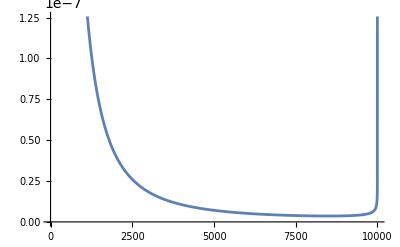

```mathematica
Plot[(10^-22(1-r/10000^2))^gd3[r]+10^-22(1-r/10000^2),{r,0,10000}]
```

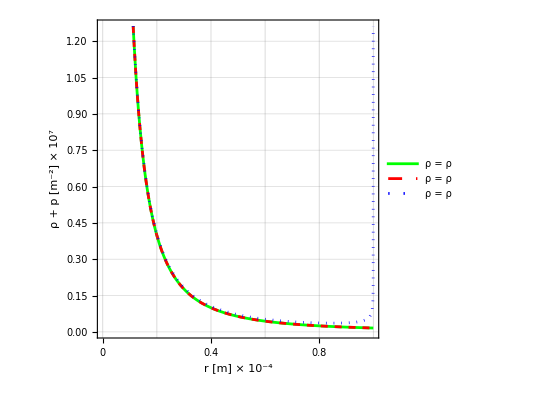

```mathematica
nullGRhoas=Plot[{((10^-22)^gd1[r]+10^-22) 10^7,((10^-22(1-r/10000))^gd2[r]+10^-22(1-r/10000)) 10^7,((10^-22(1-r/10000^2))^gd3[r]+10^-22(1-r/10000^2)) 10^7},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain] Style["× 10^-4",Plain], "ρ + p"  Style["[m^-2]",Plain] Style["× 10^7",Plain]},PlotStyle->{{Green},{Red,Dashed},{Blue,Dotted}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

## K Cases

### Γ = 1 and ρ = ρ_0

```mathematica
kd1=NDSolveValue[{(-r (1+K[r]) (Λ+4 (π+3 π K[r]) Subscript[ρ, 0])-(3+r^2 Λ-8 π r^2 Subscript[ρ, 0]) K'[r])==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22},K[0.001]==0.0001},K,{r,0.001,10000}]
```

InterpolatingFunction[…]

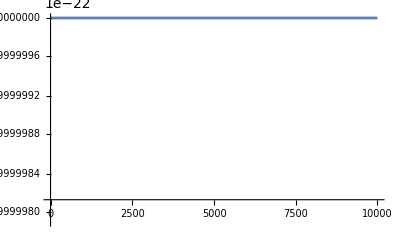

```mathematica
Plot[kd1[r] 10^-22+10^-22,{r,0,10000},PlotRange->Automatic]
```

### Γ = 1 and ρ = ρ_0(1-r/b)

```mathematica
kd2=NDSolveValue[{(-12 π (b-r)^2 r K[r]^2 Subscript[ρ, 0]+K[r] (b (3-(b-2 r) r Λ)+π r (-16 b^2+23 b r-9 r^2) Subscript[ρ, 0])+(b-r) (-b r Λ-b (3+r^2 Λ) K'[r]+π (4 b-3 r) r Subscript[ρ, 0] (-1+2 r K'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},K[0.001]==0.0001},K,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

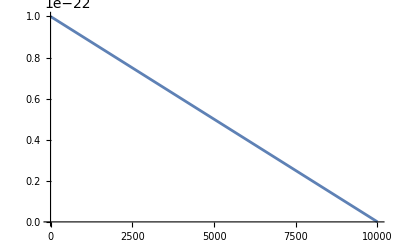

```mathematica
Plot[kd2[r](10^-22(1-r/10000))+10^-22(1-r/10000),{r,0,10000}]
```

### Γ = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
kd3=NDSolveValue[{(-60 π r (b^2-r^2)^2 K[r]^2 Subscript[ρ, 0]+r K[r] (5 b^2 (6-b^2 Λ+3 r^2 Λ)-8 π (10 b^4-9 b^2 r^2+3 r^4) Subscript[ρ, 0])-(b-r) (b+r) (4 π r (-5 b^2+3 r^2) Subscript[ρ, 0] (-1+2 r K'[r])+5 b^2 (r Λ+(3+r^2 Λ) K'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},K[0.001]==0.0001},K,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

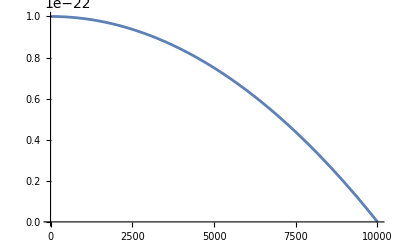

```mathematica
Plot[kd3[r](10^-22(1-r^2/10000^2))+10^-22(1-r^2/10000^2),{r,0,10000}]
```

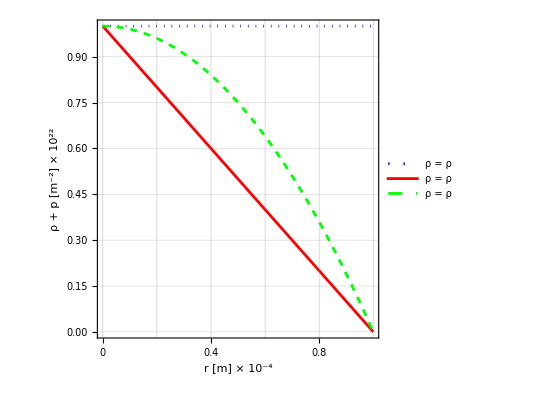

```mathematica
nullKRhoas=Plot[{(kd1[r] 10^-22+10^-22) 10^22,(kd2[r](10^-22(1-r/10000))+10^-22(1-r/10000)) 10^22,(kd3[r](10^-22(1-r^2/10000^2))+10^-22(1-r^2/10000^2)) 10^22},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain] Style["× 10^-4",Plain], "ρ + p"  Style["[m^-2]",Plain] Style["× 10^22",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Bottom}],GridLines->Automatic,AspectRatio->1]
```

## Weak Conditions

```mathematica
(*For this we use 8πρ - Λ ≥ 0, for each case*)
```

## Mass Cases

### Γ = 1 and K = 1

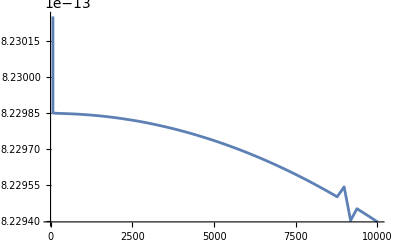

```mathematica
Plot[8π(mp1[r]/(4π r^2))-10^-52,{r,0,10000}]
```

### K = r, Γ = 1

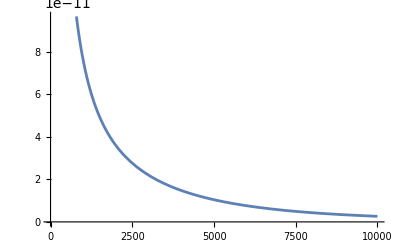

```mathematica
Plot[8π(mp2[r]/(4π r^2))-10^-52,{r,0,10000}]
```

### K = r/b, Γ = 1

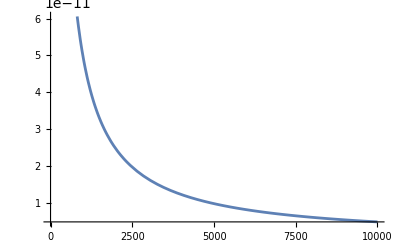

```mathematica
Plot[8π(mp3[r]/(4π r^2))-10^-52,{r,0,10000}]
```

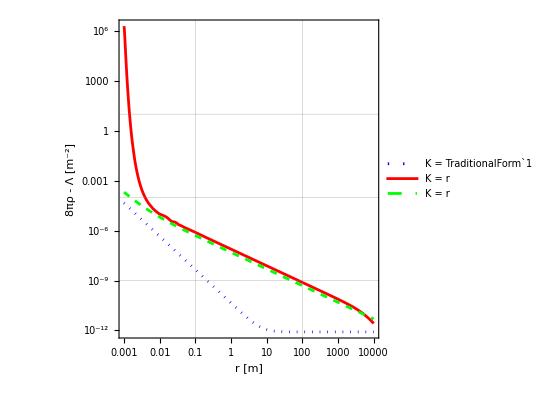

```mathematica
weakdenKas=LogLogPlot[{(8π(mp1[r]/(4π r^2))-10^-52),(8π(mp2[r]/(4π r^2))-10^-52),(8π(mp3[r]/(4π r^2))-10^-52)},{r,0.001,10000},FrameTicks->{{All,None},{All,None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain], "8πρ - Λ"  Style["[m^-2]",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = TraditionalForm`1","K = r","K = r"},{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["weakdenKas.pdf",weakdenKas]
```

weakdenKas.pdf

## Γ Cases

```mathematica
(*This case is trivial because Γ does not effect density in our EOS*)
```

### K = 1 and ρ = ρ_0

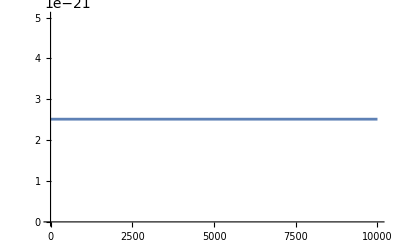

```mathematica
Plot[8π (10^-22)-10^-52,{r,0,10000}]
```

### K = 1 and ρ = ρ_0(1-r/b)

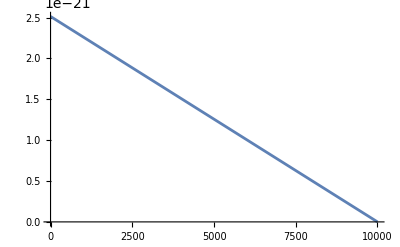

```mathematica
Plot[8π (10^-22(1-r/10000))-10^-52,{r,0,10000}]
```

### K = 1 and ρ = ρ_0(1-r^2/b^2)

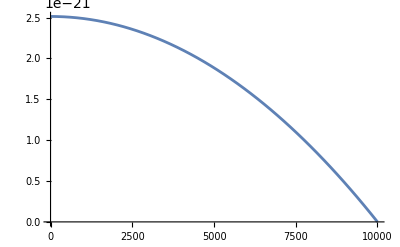

```mathematica
Plot[8π (10^-22(1-r^2/10000^2))-10^-52,{r,0,10000}]
```

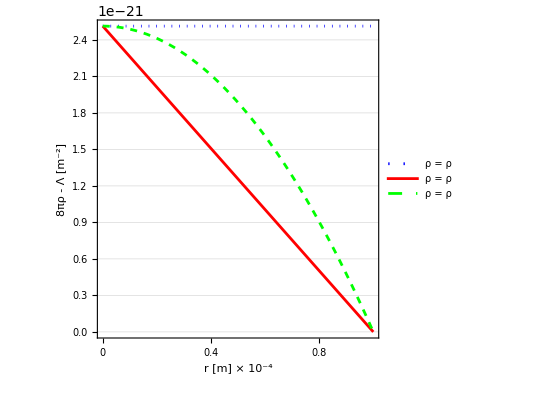

```mathematica
weakDenas=Plot[{8π (10^-22)-10^-52,8π (10^-22(1-r/10000))-10^-52,8π (10^-22(1-r^2/10000^2))-10^-52},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain] Style["× 10^-4",Plain], "8πρ - Λ"  Style["[m^-2]",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Bottom}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["weakDenas.pdf",weakDenas]
```

weakDenas.pdf

## K Cases

```mathematica
(*The same applies to our K parameter. In our EOS K does not effect density*)
```

### Γ = 1 and ρ = ρ_0

### Γ = 1 and ρ = ρ_0(1-r/b)

### Γ = 1 and ρ = ρ_0(1-r^2/b^2)

## Dominant Conditions

```mathematica
(*We use the equation 4π(ρ-p) - Λ ≥ 0, for each case*)
```

## Mass Cases

### Γ = 1 and K = 1

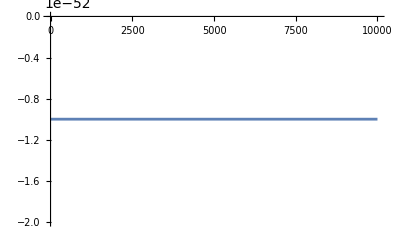

```mathematica
Plot[4π(mp1[r]/(4π r^2)-(mp1[r]/(4π r^2)))-10^-52,{r,0,10000}]
```

### K = r, Γ = 1

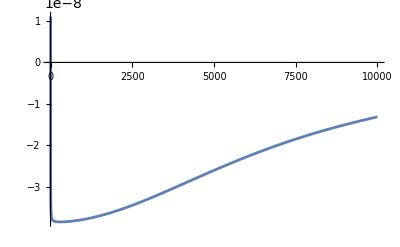

```mathematica
Plot[4π(mp2[r]/(4π r^2)-(r(mp2[r]/(4π r^2))))-10^-52,{r,0,10000}]
```

### K = r/b, Γ = 1

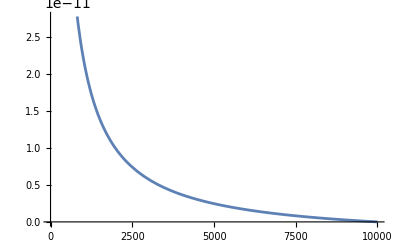

```mathematica
Plot[4π(mp3[r]/(4π r^2)-(r/10000(mp3[r]/(4π r^2))))-10^-52,{r,0,10000}]
```

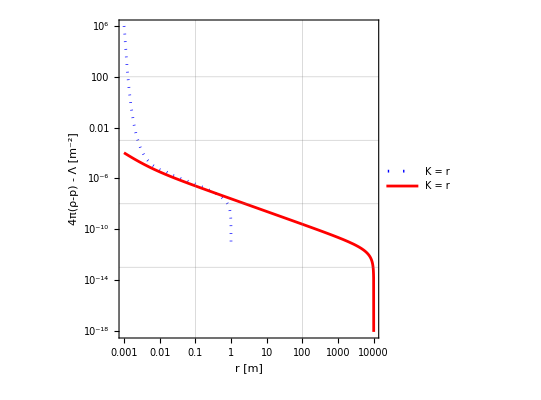

```mathematica
domdenKas=LogLogPlot[{(4π(mp2[r]/(4π r^2)-(r(mp2[r]/(4π r^2))))-10^-52),(4π(mp3[r]/(4π r^2)-(r/10000(mp3[r]/(4π r^2))))-10^-52)},{r,0.001,10000},FrameTicks->{{All,None},{All,None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain], "4π(ρ-p) - Λ"  Style["[m^-2]",FontSlant->Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = r","K = r"},{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["domdenKas.pdf",domdenKas]
```

domdenKas.pdf

## Γ Cases

### K = 1 and ρ = ρ_0

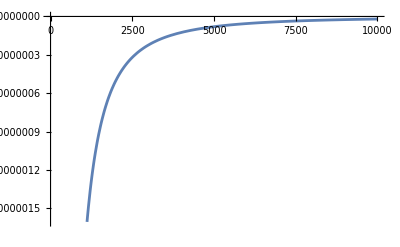

```mathematica
Plot[4π(10^-22-(10^-22)^gd1[r])-10^-52,{r,0,10000}]
```

### K = 1 and ρ = ρ_0(1-r/b)

```mathematica
Plot[4π(10^-22(1-r/10000)-(10^-22(1-r/10000))^gd2[r])-10^-52,{r,0,10000}]
```

-Graphics-

### K = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
Plot[4π(10^-22(1-r^2/10000^2)-(10^-22(1-r^2/10000^2))^gd3[r])-10^-52,{r,0,10000}]
```

-Graphics-

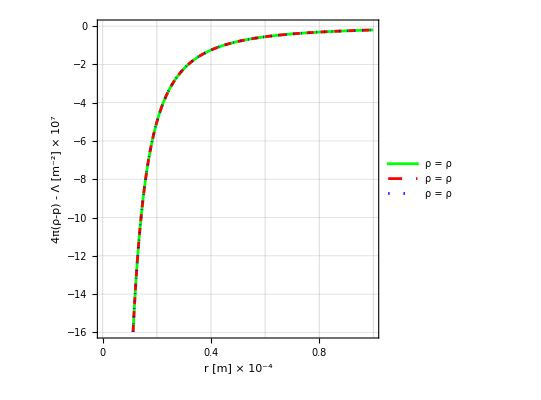

```mathematica
domGdensas=Plot[{(4π(10^-22-(10^-22)^gd1[r])-10^-52) 10^7,(4π(10^-22(1-r/10000)-(10^-22(1-r/10000))^gd2[r])-10^-52) 10^7,(4π(10^-22(1-r^2/10000^2)-(10^-22(1-r^2/10000^2))^gd3[r])-10^-52) 10^7},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain] Style["× 10^-4",Plain], "4π(ρ-p) - Λ"  Style["[m^-2]",FontSlant->Plain] Style["× 10^7",Plain]},PlotStyle->{{Green},{Red,Dashed},{Blue,Dotted}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Right,Bottom}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["domGdensas.pdf",domGdensas]
```

domGdensas.pdf

## K Cases

### Γ = 1 and ρ = ρ_0

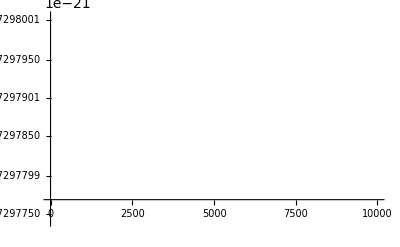

```mathematica
Plot[4π(10^-22-(kd1[r] 10^-22))-10^-52,{r,0,10000}]
```

### Γ = 1 and ρ = ρ_0(1-r/b)

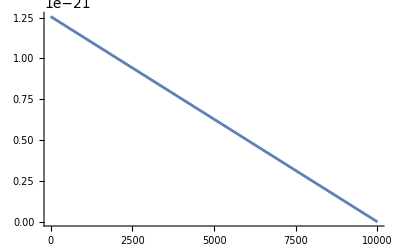

```mathematica
Plot[4π(10^-22(1-r/10000)-kd2[r](10^-22(1-r/10000)))-10^-52,{r,0,10000}]
```

### Γ = 1 and ρ = ρ_0(1-r^2/b^2)

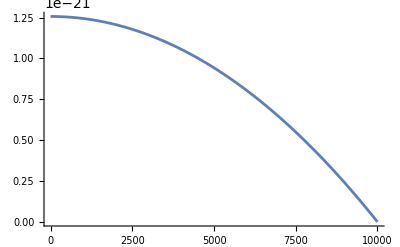

```mathematica
Plot[4π(10^-22(1-r^2/10000^2)-kd3[r](10^-22(1-r^2/10000^2)))-10^-52,{r,0,10000}]
```

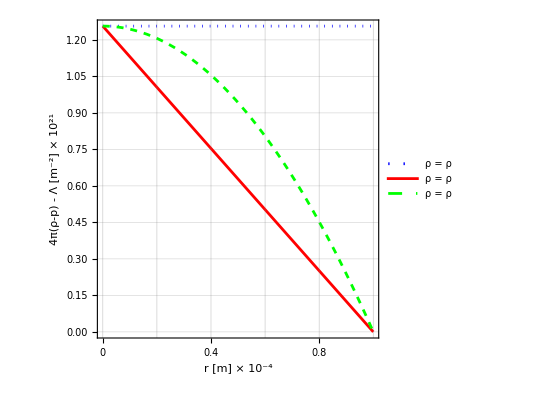

```mathematica
domKdenas=Plot[{(4π(10^-22-(kd1[r] 10^-22))-10^-52) 10^21,(4π(10^-22(1-r/10000)-kd2[r](10^-22(1-r/10000)))-10^-52) 10^21,(4π(10^-22(1-r^2/10000^2)-kd3[r](10^-22(1-r^2/10000^2)))-10^-52) 10^21},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain] Style["× 10^-4",Plain], "4π(ρ-p) - Λ"  Style["[m^-2]",FontSlant->Plain] Style["× 10^21",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Bottom}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["domKdenas.pdf",domKdenas]
```

domKdenas.pdf

## Strong Conditions

```mathematica
(*We use the equation 4π(ρ + 3p) - Λ ≥ 0, for each case*)
```

## Mass Cases

### Γ = 1 and K = 1

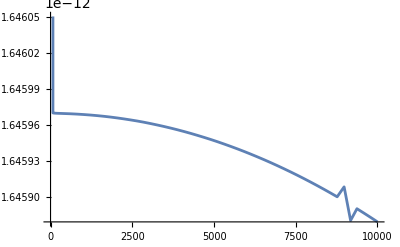

```mathematica
Plot[4π(mp1[r]/(4π r^2)+3(mp1[r]/(4π r^2)))-10^-52,{r,0,10000}]
```

### K = r, Γ = 1

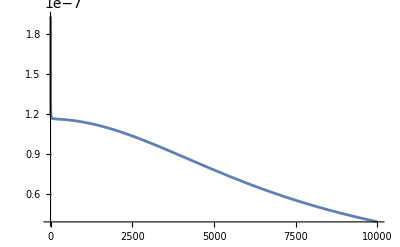

```mathematica
Plot[4π(mp2[r]/(4π r^2)+3(r(mp2[r]/(4π r^2))))-10^-52,{r,0,10000}]
```

### K = r/b, Γ = 1

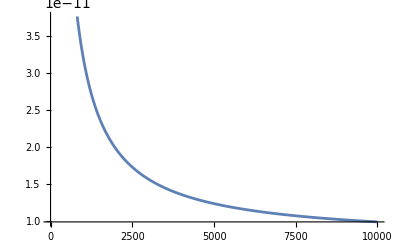

```mathematica
Plot[4π(mp3[r]/(4π r^2)+3(r/10000(mp3[r]/(4π r^2))))-10^-52,{r,0,10000}]
```

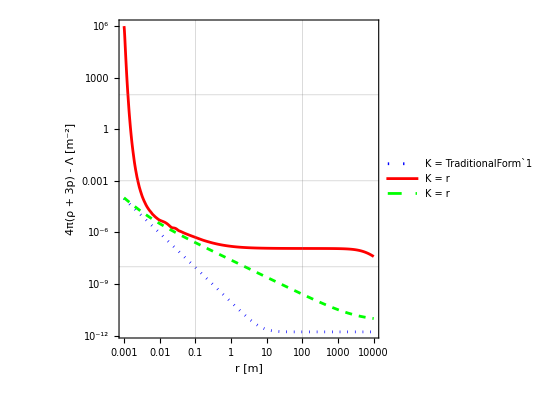

```mathematica
strongdenKas=LogLogPlot[{(4π(mp1[r]/(4π r^2)+3(mp1[r]/(4π r^2)))-10^-52),(4π(mp2[r]/(4π r^2)+3(r(mp2[r]/(4π r^2))))-10^-52),(4π(mp3[r]/(4π r^2)+3(r/10000(mp3[r]/(4π r^2))))-10^-52)},{r,0.001,10000},FrameTicks->{{All,None},{All,None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain], "4π(ρ + 3p) - Λ"  Style["[m^-2]",FontSlant->Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = TraditionalForm`1","K = r" ,"K = r"},{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["strongdenKas.pdf",strongdenKas]
```

strongdenKas.pdf

## Γ Cases

### K = 1 and ρ = ρ_0

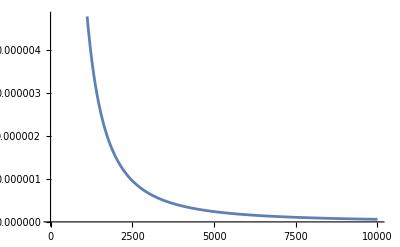

```mathematica
Plot[4π(10^-22+3(10^-22)^gd1[r])-10^-52,{r,0,10000}]
```

### K = 1 and ρ = ρ_0(1-r/b)

```mathematica
Plot[4π(10^-22(1-r/10000)+3(10^-22(1-r/10000))^gd2[r])-10^-52,{r,0,10000}]
```

-Graphics-

### K = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
Plot[4π(10^-22(1-r^2/10000^2)+3(10^-22(1-r^2/10000^2))^gd3[r])-10^-52,{r,0,10000}]
```

-Graphics-

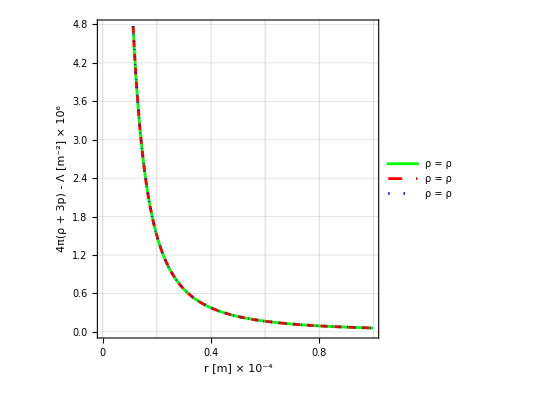

```mathematica
strongGrhoas=Plot[{(4π(10^-22+3(10^-22)^gd1[r])-10^-52) 10^6,(4π(10^-22(1-r/10000)+3(10^-22(1-r/10000))^gd2[r])-10^-52) 10^6,(4π(10^-22(1-r^2/10000^2)+3(10^-22(1-r^2/10000^2))^gd3[r])-10^-52) 10^6},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain] Style["× 10^-4",Plain], "4π(ρ + 3p) - Λ"  Style["[m^-2]",FontSlant->Plain] Style["× 10^6",Plain]},PlotStyle->{{Green},{Red,Dashed},{Blue,Dotted}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["strongGrhoas.pdf",strongGrhoas]
```

strongGrhoas.pdf

## K Cases

### Γ = 1 and ρ = ρ_0

```mathematica
Plot[4π(10^-22+3(kd1[r] 10^-22))-10^-52,{r,0,10000}]
```

-Graphics-

### Γ = 1 and ρ = ρ_0(1-r/b)

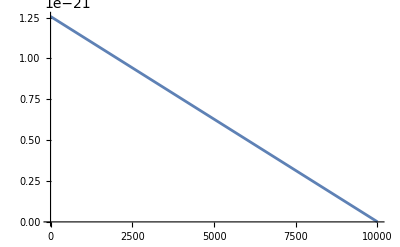

```mathematica
Plot[4π(10^-22(1-r/10000)+3(kd2[r] 10^-22(1-r/10000)))-10^-52,{r,0,10000}]
```

### Γ = 1 and ρ = ρ_0(1-r^2/b^2)

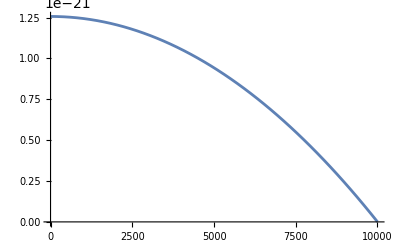

```mathematica
Plot[4π(10^-22(1-r^2/10000^2)+3(kd3[r] 10^-22(1-r^2/10000^2)))-10^-52,{r,0,10000}]
```

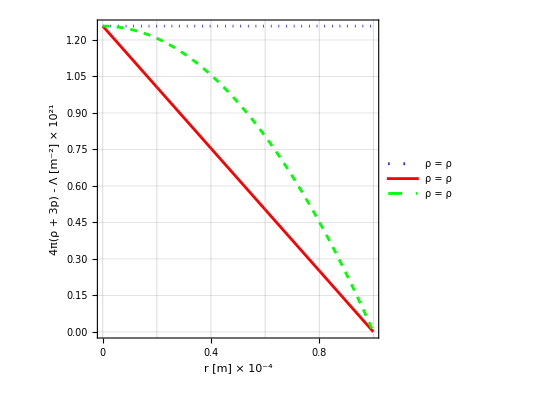

```mathematica
strongKrhoas=Plot[{(4π(10^-22+3(kd1[r] 10^-22))-10^-52) 10^21,(4π(10^-22(1-r/10000)+3(kd2[r] 10^-22(1-r/10000)))-10^-52) 10^21,(4π(10^-22(1-r^2/10000^2)+3(kd3[r] 10^-22(1-r^2/10000^2)))-10^-52) 10^21},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain] Style["× 10^-4",Plain], "4π(ρ + 3p) - Λ"  Style["[m^-2]",FontSlant->Plain] Style["× 10^21",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Bottom}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["strongKrhoas.pdf",strongKrhoas]
```

strongKrhoas.pdf

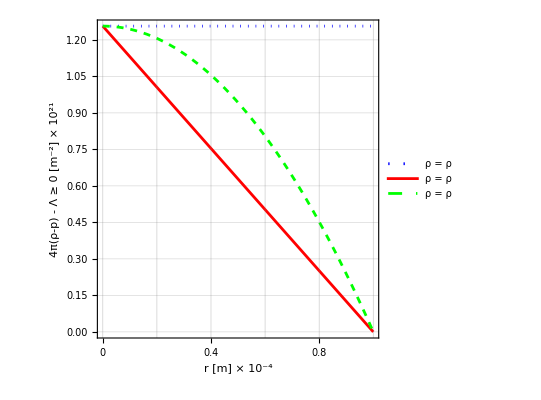

```mathematica
Plot[{(4π(10^-22-(kd1[r] 10^-22))-10^-52) 10^21,(4π(10^-22(1-r/10000)-kd2[r](10^-22(1-r/10000)))-10^-52) 10^21,(4π(10^-22(1-r^2/10000^2)-kd3[r](10^-22(1-r^2/10000^2)))-10^-52) 10^21},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",FontSlant->Plain] Style["× 10^-4",Plain], "4π(ρ-p) - Λ ≥ 0"  Style["[m^-2]",FontSlant->Plain] Style["× 10^21",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
(*No Titles, change Gc into m, no inequality signs, try loglog for plots that are indivually scaled, write nores in the notebook, *)
```